```mathematica
Module[{fx,fy,p1,yellow,orange},
fx=(1-Cos[θ])*Sin[θ]*Cos[ϕ];
fy=1.85*Cos[θ];

p1=Show[Table[
ParametricPlot[{{fx+6.9*n,fy},{0.7*fx+6.9*n,0.7*fy-0.6}},{θ,0,2 π},{ϕ,0,2 π},
PlotRange->{{-2,22.5},{-2.55,2}},
PlotStyle->{{Opacity[1],Darker[Yellow,0.1]},{Opacity[1],Orange}},
BoundaryStyle->{Opacity[0.7],Red}],
{n,0,3}],ImageSize->150,Axes->False,Frame->False];

yellow=Table[Table[{fx+6.9*n,fy},{{θ,0,2 π},{ϕ,0,2 π}}],{n,0,3,1}]

]
```

Table::write: Tag List in {θ, 0, 2\ π} is Protected.

General::stop: Further output of Table :: write will be suppressed during this calculation.

{Table[{fx$11196+6.9 n,fy$11196},{{θ,0,2 π},{ϕ,0,2 π}}],Table[{fx$11196+6.9 n,fy$11196},{{θ,0,2 π},{ϕ,0,2 π}}],Table[{fx$11196+6.9 n,fy$11196},{{θ,0,2 π},{ϕ,0,2 π}}],Table[{fx$11196+6.9 n,fy$11196},{{θ,0,2 π},{ϕ,0,2 π}}]}

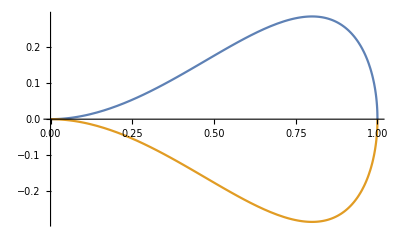

```mathematica
Module[{n},
n=4;
Plot[{√(x^n*(1-x)),-√(x^n*(1-x))},{x,0,1}]
]
```

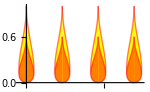

```mathematica
(*list1=Table[{√(x^4*(1-x)),-x},{x,0,1,0.01}];
list2=Table[{-√(x^4*(1-x)),-x},{x,0,1,0.01}];
ListPlot[{list1,list2},Joined->True,PlotStyle->{{Thick,Opacity[0.5,Red]}},AspectRatio->Full,Filling->Axis,FillingStyle->Opacity[1,Yellow]]*)
list1=Quiet@Table[{5*√(x^4*(1-x))+6.9*n,-x+1},{x,0,1,0.01}];
list2=Quiet@Table[{-5*√(x^4*(1-x))+6.9*n,-x+1},{x,0,1,0.01}];
list3=Quiet@Table[{5*√(x^4*(1-x))+6.9*n,0.6*(-x+1)},{x,0,1,0.01}];
list4=Quiet@Table[{-5*√(x^4*(1-x))+6.9*n,0.6*(-x+1)},{x,0,1,0.01}];
heat=Show[
Table[ListPlot[{list1,list2},Joined->True,PlotStyle->{{Thick,Opacity[0.5,Red]}},Filling->Axis,FillingStyle->Opacity[1,Yellow]],
{n,0,3,1}],
Table[ListPlot[{list3,list4},Joined->True,PlotStyle->{{Thick,Opacity[0.5,Red]}},Filling->Axis,FillingStyle->Opacity[1,Orange]],
{n,0,3,1}],
PlotRange->{0,2},ImageSize->150]
```